```mathematica
en = -0.6;
Em1= -0.579125;
Em2 =-0.603125;
f=-3*Log[2]
g=(en-Em1)/(Em1-Em2)
Exp[f*g]
```

-3 Log[2]

-0.869792

6.10239

```mathematica
(-0.5-Em1)/(Em1-Em2)
```

3.29687

```mathematica
rm =1;
l[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
sum[a_]:=4 l[a]+4 l[a √2] + 4 l[2a]+ 8 l[√5 a]+4 l[2 √2 a]
FindMinimum[sum[a],a]
```

{-5.28465,{a→0.978351}}

```mathematica
FindMinimum[myFun,{r, 0.5}]
```

FindMinimum::nrnum: The function value myFun is not a real number at {r} = {0.5}.

FindMinimum[myFun,{r,0.5}]

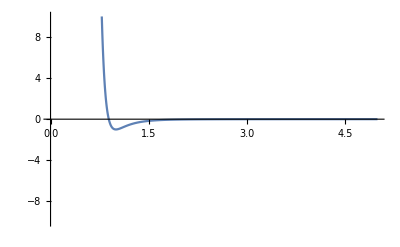

```mathematica
Plot[fun[r], {r, 0, 5}, PlotRange->{-10,10}]
```

```mathematica
FindMinimum[x Cos[x],{x,2}]
```

{-3.28837,{x→3.42562}}

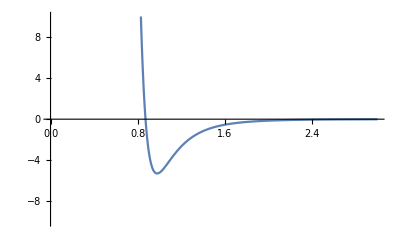

```mathematica
Plot[sum[a], {a, 0, 3}, PlotRange->{-10,10}]
```

```mathematica
sumA[a_]:=4 l[a]+4 l[a √2] + 4 l[2a]
sumB[a_,b_,c_, d_]:=4 l[a]+4 l[b √2] + 4 l[2c]+ 8 l[√5 d]
```

```mathematica
FindMinimum[sumA[a],a]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{-5.12281,{a→0.98088}}

```mathematica
FindMinimum[sumB[a,b,c,d],{a,b,c,d}]
```

{-20.,{a→1.,b→0.707107,c→0.5,d→0.447214}}

```mathematica
rm =1;
V[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
n = 5;
ex = {1,0,0};
ey = {0,1,0};
ez = {0,0,1};
a1=(a/2)*(ex+ey);
a2=(a/2)*(ey+ez);
a3=(a/2)*(ex+ez);

pot = 0;
For[i=0,i<n,i++,
iplus1 = If[i==n-1, 0, i+1 ];
imins1 = If[i==0, n-1, i-1 ];

For[j=0,j<n,j++,
jplus1 = If[j==n-1, 0, j+1 ];
jmins1 = If[j==0, n-1, j-1 ];

For[k=0,k<n,k++,
kplus1 = If[k==n-1, 0, k+1 ];
kmins1 = If[k==0, n-1, k-1 ];

(*rc=(i*n*n)*a1+(j*n)*a2+k*a3;
r1=(iplus1*n*n)*a1+(j*n)*a2+k*a3;
r2=(imins1*n*n)*a1+(j*n)*a2+k*a3;
r3=(i*n*n)*a1+(jplus1*n)*a2+k*a3;
r4=(i*n*n)*a1+(jmins1*n)*a2+k*a3;
r5=(i*n*n)*a1+(j*n)*a2+kplus1*a3;
r6=(i*n*n)*a1+(j*n)*a2+kmins1*a3;*)

rc=i*a1+j*a2+k*a3;
r1=iplus1*a1+j*a2+k*a3;
r2=imins1*a1+j*a2+k*a3;
r3=i*a1+jplus1*a2+k*a3;
r4=i*a1+jmins1*a2+k*a3;
r5=i*a1+j*a2+kplus1*a3;
r6=i*a1+j*a2+kmins1*a3;

pot+=V[Norm[rc-r1]]+V[Norm[rc-r2]]+V[Norm[rc-r3]]+V[Norm[rc-r4]]+V[Norm[rc-r5]]+V[Norm[rc-r6]];


]
]
]
```

```mathematica
pot
```

5033164875/(131072 Abs[a]^12)-1228875/(128 Abs[a]^6)

```mathematica
energy[a_]:=5033164875/(131072 a^12)-1228875/(128 a^6);
FindMinimum[energy[a],a]
```

{-600.073,{a→1.4142}}

```mathematica
N[√2]
```

1.41421

```mathematica
N[energy[√2]/2]
```

-300.037

```mathematica
rm =1;
V[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
n = 5;
ex = {1,0,0};
ey = {0,1,0};
ez = {0,0,1};
a1=(√2/2)*(ex+ey);
a2=(√2/2)*(ey+ez);
a3=(√2/2)*(ex+ez);

pot = 0;
For[i=0,i<n,i++,
iplus1 = If[i==n-1, 0, i+1 ];
imins1 = If[i==0, n-1, i-1 ];

For[j=0,j<n,j++,
jplus1 = If[j==n-1, 0, j+1 ];
jmins1 = If[j==0, n-1, j-1 ];

For[k=0,k<n,k++,
kplus1 = If[k==n-1, 0, k+1 ];
kmins1 = If[k==0, n-1, k-1 ];

(*rc=(i*n*n)*a1+(j*n)*a2+k*a3;
r1=(iplus1*n*n)*a1+(j*n)*a2+k*a3;
r2=(imins1*n*n)*a1+(j*n)*a2+k*a3;
r3=(i*n*n)*a1+(jplus1*n)*a2+k*a3;
r4=(i*n*n)*a1+(jmins1*n)*a2+k*a3;
r5=(i*n*n)*a1+(j*n)*a2+kplus1*a3;
r6=(i*n*n)*a1+(j*n)*a2+kmins1*a3;*)

rc=i*a1+j*a2+k*a3;
r1=iplus1*a1+j*a2+k*a3;
r2=imins1*a1+j*a2+k*a3;
r3=i*a1+jplus1*a2+k*a3;
r4=i*a1+jmins1*a2+k*a3;
r5=i*a1+j*a2+kplus1*a3;
r6=i*a1+j*a2+kmins1*a3;

Print[ N[rc]]

]
]
]
```

```mathematica
rm =1;
V[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
n = 1;
ex = {1,0,0};
ey = {0,1,0};
ez = {0,0,1};
a1=(a/2)*(ex+ey);
a2=(a/2)*(ey+ez);
a3=(a/2)*(ex+ez);

nAtoms = n^3;
superR = Table[Subscript[x, i]^2,{i,3*nAtoms}];

pot = 0;
For[i=0,i<n,i++,
iplus1 = If[i==n-1, 0, i+1 ];
imins1 = If[i==0, n-1, i-1 ];

For[j=0,j<n,j++,
jplus1 = If[j==n-1, 0, j+1 ];
jmins1 = If[j==0, n-1, j-1 ];

For[k=0,k<n,k++,
kplus1 = If[k==n-1, 0, k+1 ];
kmins1 = If[k==0, n-1, k-1 ];

pc=(i*n*n)+(j*n)+k;
p1=(iplus1*n*n)+(j*n)+k;
p2=(imins1*n*n)+(j*n)+k;
p3=(i*n*n)+(jplus1*n)+k;
p4=(i*n*n)+(jmins1*n)+k;
p5=(i*n*n)+(j*n)+kplus1;
p6=(i*n*n)+(j*n)+kmins1;

rc=i*a1+j*a2+k*a3;.10*
r1=iplus1*a1+j*a2+k*a3;
r2=imins1*a1+j*a2+k*a3;
r3=i*a1+jplus1*a2+k*a3;
r4=i*a1+jmins1*a2+k*a3;
r5=i*a1+j*a2+kplus1*a3;
r6=i*a1+j*a2+kmins1*a3;

pot+=V[Norm[rc-r1]]+V[Norm[rc-r2]]+V[Norm[rc-r3]]+V[Norm[rc-r4]]+V[Norm[rc-r5]]+V[Norm[rc-r6]];


]
]
]
```

```mathematica
superR = {Subscript[x, 1]}
```

```mathematica
D[Subscript[x, 1]^(1/2),Subscript[x, 1]]
```

1/(2 √x_1)

```mathematica
nAtoms = 2;
superR = Table[Subscript[x, i]^2,{i,3*nAtoms}];
superR
```

{x_1^2,x_2^2,x_3^2,x_4^2,x_5^2,x_6^2}

```mathematica
rm =1;
V[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
n = 3;
ex = {1,0,0};
ey = {0,1,0};
ez = {0,0,1};
a1=(√2/2)*(ex+ey);
a2=(√2/2)*(ey+ez);
a3=(√2/2)*(ex+ez);

pot = 0;
For[i=0,i<n,i++,
iplus1 = If[i==n-1, 0, i+1 ];
imins1 = If[i==0, n-1, i-1 ];

For[j=0,j<n,j++,
jplus1 = If[j==n-1, 0, j+1 ];
jmins1 = If[j==0, n-1, j-1 ];

For[k=0,k<n,k++,
kplus1 = If[k==n-1, 0, k+1 ];
kmins1 = If[k==0, n-1, k-1 ];

rc=i*a1+j*a2+k*a3;
r1=iplus1*a1+j*a2+k*a3;
r2=imins1*a1+j*a2+k*a3;
r3=i*a1+jplus1*a2+k*a3;
r4=i*a1+jmins1*a2+k*a3;
r5=i*a1+j*a2+kplus1*a3;
r6=i*a1+j*a2+kmins1*a3;

s1 = V[Norm[rc-r1]];
s2 = V[Norm[rc-r2]];
s3 = V[Norm[rc-r3]];
s4 = V[Norm[rc-r4]];
s5 = V[Norm[rc-r5]];
s6 = V[Norm[rc-r6]];

Print[N[s1], N[s2], N[s3], N[s4], N[s5], N[s6]];
pot+=s1 + s2 +s3 +s4+s5+s6;

(*pot+=V[Norm[rc-r1]]+V[Norm[rc-r2]]+V[Norm[rc-r3]]+V[Norm[rc-r4]]+V[Norm[rc-r5]]+V[Norm[rc-r6]];*)


]
]
]

Simplify[pot]
N[pot]
```

-1.-0.0310059-1.-0.0310059-1.-0.0310059

-1.-0.0310059-1.-0.0310059-1.-1.

-1.-0.0310059-1.-0.0310059-0.0310059-1.

-1.-0.0310059-1.-1.-1.-0.0310059

-1.-0.0310059-1.-1.-1.-1.

-1.-0.0310059-1.-1.-0.0310059-1.

-1.-0.0310059-0.0310059-1.-1.-0.0310059

-1.-0.0310059-0.0310059-1.-1.-1.

-1.-0.0310059-0.0310059-1.-0.0310059-1.

-1.-1.-1.-0.0310059-1.-0.0310059

-1.-1.-1.-0.0310059-1.-1.

-1.-1.-1.-0.0310059-0.0310059-1.

-1.-1.-1.-1.-1.-0.0310059

-1.-1.-1.-1.-1.-1.

-1.-1.-1.-1.-0.0310059-1.

-1.-1.-0.0310059-1.-1.-0.0310059

-1.-1.-0.0310059-1.-1.-1.

-1.-1.-0.0310059-1.-0.0310059-1.

-0.0310059-1.-1.-0.0310059-1.-0.0310059

-0.0310059-1.-1.-0.0310059-1.-1.

-0.0310059-1.-1.-0.0310059-0.0310059-1.

-0.0310059-1.-1.-1.-1.-0.0310059

-0.0310059-1.-1.-1.-1.-1.

-0.0310059-1.-1.-1.-0.0310059-1.

-0.0310059-1.-0.0310059-1.-1.-0.0310059

-0.0310059-1.-0.0310059-1.-1.-1.

-0.0310059-1.-0.0310059-1.-0.0310059-1.

-224613/2048

-109.674

```mathematica
FindMinimum[3072/a^12-768/a^6, a]
```

{-48.,{a→1.41421}}

```mathematica
FindMinimum[221211/(32 a^12)-3483/(2 a^6),a]
```

{-109.681,{a→1.41241}}

31.6743

```mathematica
H=({{x^2, x y, x z, -x^2, -x y, -x z}, {y x, y^2, y z, -y x, -y^2, -y z}, {z x, z y, z^2, -z x, -z y, -z^2}, {-x^2, -x y, -x z, x^2, x y, x z}, {-y x, -y^2, -y z, y x, y^2, y z}, {-z x, -z y, -z^2, z x, z y, z^2}});
Eigenvalues[H]
Simplify[%]
```

{0,0,0,0,0,2 (x^2+y^2+z^2)}

{0,0,0,0,0,2 (x^2+y^2+z^2)}

```mathematica
n =2;
Subscript[e, 1] = {1,0,0};
Subscript[e, 2] = {0,1,0};
Subscript[e, 3] = {0,0,1};
a1=(√2/2)*(ex+ey);
a2=(√2/2)*(ey+ez);
a3=(√2/2)*(ex+ez);

posAtoms = {};
For[i=0,i<n,i++,
iplus1 = If[i==n-1, 0, i+1 ];
imins1 = If[i==0, n-1, i-1 ];

For[j=0,j<n,j++,
jplus1 = If[j==n-1, 0, j+1 ];
jmins1 = If[j==0, n-1, j-1 ];

For[k=0,k<n,k++,
kplus1 = If[k==n-1, 0, k+1 ];
kmins1 = If[k==0, n-1, k-1 ];

rc=i*a1+j*a2+k*a3;
posAtoms=Append[posAtoms,rc]


]
]
]
posAtoms
```

{{0,0,0},{1/(√2),0,1/(√2)},{0,1/(√2),1/(√2)},{1/(√2),1/(√2),√2},{1/(√2),1/(√2),0},{√2,1/(√2),1/(√2)},{1/(√2),√2,1/(√2)},{√2,√2,√2}}

```mathematica
ClearAll
nAtoms = 2;
Subscript[e, 1] = {1,0,0};
Subscript[e, 2] = {0,1,0};
Subscript[e, 3] = {0,0,1};


indxP[s_]:=QuotientRemainder[s-1,3]⟦1⟧+1;
indxI[s_]:=QuotientRemainder[s-1,3]⟦2⟧+1;

diffPQ[s_,t_]:=posAtoms⟦indxP[s]⟧- posAtoms⟦indxP[t]⟧;

u[s_,t_]:= If[indxP[s]≠indxP[t],diffPQ[s,t]/Norm[diffPQ[s,t]], {0,0,0}];
eunit[s_]:=Subscript[e, indxI[s]]



h[s_,t_]:=Dot[eunit[s],u[s,t]] Dot[eunit[t],u[s,t]] ;

H=Table[ h[i,j],{i,3nAtoms},{j,3nAtoms}];
H//MatrixForm
```

ClearAll

(0 | 0 | 0 | 1/2 | 0 | 1/2
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/2 | 0 | 1/2
1/2 | 0 | 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
1/2 | 0 | 1/2 | 0 | 0 | 0)

```mathematica
Eigenvalues[H]
```

{-1,1,0,0,0,0}

```mathematica
ClearAll;

Clear[x1,x2,R,V,VV,Vcart]
rm =1;

(*R[v1_,v2_,v3_, v4_, v5_, v6_]:=  √((v1-v4 )^2+(v2-v5)^2+(v3-v6)^2) ;*)
R[v1_,v2_,v3_, v4_, v5_, v6_,dx_, dy_, dz_]:=  √((v1-(v4+dx) )^2+(v2-(v5+dy))^2+(v3-(v6+dz))^2) ;

V[r_]:=-2 ((rm/r)^6) + (rm/r)^12;
VV[d_]:=-1+36(d/rm)^2;

Vcart[v1_,v2_,v3_, v4_, v5_, v6_, dx_,dy_,dz_]:=-2 ((rm/R[v1,v2,v3, v4, v5, v6, dx,dy,dz])^6) + (rm/R[v1,v2,v3, v4, v5, v6, dx,dy,dz])^12;


n = 2;
Subscript[e, 1] = {1,0,0};
Subscript[e, 2] = {0,1,0};
Subscript[e, 3] = {0,0,1};
Subscript[a, 1]=(√2/2)*(ex+ey);
Subscript[a, 2]=(√2/2)*(ey+ez);
Subscript[a, 3]=(√2/2)*(ex+ez);
Subscript[A, 1]=n Subscript[a, 1];
Subscript[A, 2]=n Subscript[a, 1];
Subscript[A, 3]=n Subscript[a, 2];
Subscript[A, 4]=n Subscript[a, 2];
Subscript[A, 5]=n Subscript[a, 3];
Subscript[A, 6]=n Subscript[a, 3];

getIplus1[i_,n_]:= If[ i==n-1, 0,        i+1];
getImins1[i_,n_]:= If[ i==0,        n-1, i-1];
getIRp1[i_,n_]:=     If[ i==n-1,   1, 0];
getIRm1[i_,n_]:=     If[ i==0,        -1, 0];

getIndxAtom[i_,j_,k_,n_]:=i*n*n  + j*n + k;
getAbsIndx[l_, m_]:=l*3 + m; (*m = 1,2,3 = x,y,z *)

makeNewVariable[numberOfx_]:=Symbol["x"<>ToString[numberOfx]];
makeS[variable_]:=ToString[variable]<>"_";

Rtot = 0;
Vtot=0;
Vtot2 = 0;
VVtot=0;


solutions = {};
variables={};
ccc={};

For[i=0,i<n,i++,
iplus1 = getIplus1[i,n];
imins1=getImins1[i,n];
iRp1=getIRp1[i,n];
iRm1=getIRm1[i,n];

For[j=0,j<n,j++,
jplus1 = getIplus1[j,n];
jmins1=getImins1[j,n];
jRp1=getIRp1[j,n];
jRm1=getIRm1[j,n];

For[k=0,k<n,k++,
kplus1 = getIplus1[k,n];
kmins1=getImins1[k,n];
kRp1=getIRp1[k,n];
kRm1=getIRm1[k,n];



Subscript[L, 0]=getIndxAtom[i,j,k,n];
Subscript[L, 1]=getIndxAtom[iplus1,j,k,n];
Subscript[L, 2]=getIndxAtom[imins1,j,k,n];
Subscript[L, 3]=getIndxAtom[i,jplus1,k,n];
Subscript[L, 4]=getIndxAtom[i,jmins1,k,n];
Subscript[L, 5]=getIndxAtom[i,j,kplus1,n];
Subscript[L, 6]=getIndxAtom[i,j,kmins1,n];



Subscript[d, 1]=iRp1;
Subscript[d, 2]=iRm1;
Subscript[d, 3]=jRp1;
Subscript[d, 4]=jRm1;
Subscript[d, 5]=kRp1;
Subscript[d, 6]=kRm1;

nx1 = getAbsIndx[Subscript[L, 0], 0];
ny1 = getAbsIndx[Subscript[L, 0], 1];
nz1= getAbsIndx[Subscript[L, 0], 2];



Subscript[r, 0]=i*Subscript[a, 1]+j*Subscript[a, 2]+k*Subscript[a, 3];
Subscript[r, 1]=iplus1*Subscript[a, 1]+j*Subscript[a, 2]+k*Subscript[a, 3];
Subscript[r, 2]=imins1*Subscript[a, 1]+j*Subscript[a, 2]+k*Subscript[a, 3];
Subscript[r, 3]=i*Subscript[a, 1]+jplus1*Subscript[a, 2]+k*Subscript[a, 3];
Subscript[r, 4]=i*Subscript[a, 1]+jmins1*Subscript[a, 2]+k*Subscript[a, 3];
Subscript[r, 5]=i*Subscript[a, 1]+j*Subscript[a, 2]+kplus1*Subscript[a, 3];
Subscript[r, 6]=i*Subscript[a, 1]+j*Subscript[a, 2]+kmins1*Subscript[a, 3];



(*For each neighbor: *)
For[m=1,m≤6,m++,

nx2 = getAbsIndx[Subscript[L, m], 0];
ny2 = getAbsIndx[Subscript[L, m], 1];
nz2= getAbsIndx[Subscript[L, m], 2];

dx= Dot[Subscript[d, m] Subscript[A, m], Subscript[e, 1]];
dy= Dot[Subscript[d, m] Subscript[A, m], Subscript[e, 2]];
dz= Dot[Subscript[d, m] Subscript[A, m], Subscript[e, 3]];

xx1=Subscript[x, nx1];
yy1=Subscript[x, ny1];
zz1=Subscript[x, nz1];
xx2=Subscript[x, nx2];
yy2=Subscript[x, ny2];
zz2=Subscript[x, nz2];

vx1=makeNewVariable[nx1];
vy1=makeNewVariable[ny1];
vz1=makeNewVariable[nz1];
vx2=makeNewVariable[nx2];
vy2=makeNewVariable[ny2];
vz2=makeNewVariable[nz2];

(*Rtot +=R[Subscript[x, nx1],Subscript[x, ny1],Subscript[x, nz1], Subscript[x, nx2], Subscript[x, ny2], Subscript[x, nz2], dx,dy, dz ];*)
Rtot +=         R[vx1,vy1,vz1,vx2,vy2,vz2,dx,dy,dz ];
Vtot += V[   R[vx1,vy1,vz1,vx2,vy2,vz2,dx,dy,dz ]   ];
(*variables =  Union[variables ,{Subscript[x, nx1],Subscript[x, ny1],Subscript[x, nz1], Subscript[x, nx2], Subscript[x, ny2], Subscript[x, nz2]}];*)
variables =  Union[variables ,{vx1,vy1,vz1,vx2,vy2,vz2}];
(*ccc=Union[ccc,{makeS[vx1],makeS[vy1],makeS[vz1],makeS[vx2],makeS[vy2],makeS[vz2]}];*)


(*Verifying*)
rr1=Subscript[r, 0];
rr2=Subscript[r, m];
sx1=Dot[rr1,Subscript[e, 1]];
sy1=Dot[rr1,Subscript[e, 2]];
sz1=Dot[rr1,Subscript[e, 3]];
sx2=Dot[rr2,Subscript[e, 1]];
sy2=Dot[rr2,Subscript[e, 2]];
sz2=Dot[rr2,Subscript[e, 3]];
Vtot2 += V[ R[sx1,sy1,sz1,sx2,sy2,sz2,dx,dy,dz ] ];
(*Print[x1,y1,z1,x2,y2,z2];*)

(*solutions = Union[ solutions, { {xx1,vx1,sx1}, {yy1,vy1,sy1}, {zz1,vz1,sz1}, {xx2,vx2,sx2}, {yy2,vy2,sy2}, {zz2,vz2,sz2} }  ];
*)
solutions = Union[ solutions, { {vx1,sx1}, {vy1,sy1}, {vz1,sz1}, {vx2,sx2}, {vy2,sy2}, {vz2,sz2} }  ];

dx1=makeNewVariable[nx1];
dy1=makeNewVariable[ny1];
dz1=makeNewVariable[nz1];
dx2=makeNewVariable[nx2];
dy2=makeNewVariable[ny2];
dz2=makeNewVariable[nz2];
(*VVtot+=VV[ R[vx1-sx1,vy1-sy1,vz1-sz1,vx2-sx2,vy2-sy2,vz2-sz2,dx,dy,dz ] ];*)
VVtot+=VV[ R[dx1,dy1,dz1,dx2,dy2,dz2,dx,dy,dz ] ];

];

]
]
]

(*Simplify[Rtot]*)
```

```mathematica
solutions
```

{{x0,0},{x1,0},{x10,1/(√2)},{x11,√2},{x12,1/(√2)},{x13,1/(√2)},{x14,0},{x15,√2},{x16,1/(√2)},{x17,1/(√2)},{x18,1/(√2)},{x19,√2},{x2,0},{x20,1/(√2)},{x21,√2},{x22,√2},{x23,√2},{x3,1/(√2)},{x4,0},{x5,1/(√2)},{x6,0},{x7,1/(√2)},{x8,1/(√2)},{x9,1/(√2)}}

```mathematica
variables
```

{x0,x1,x10,x11,x12,x13,x14,x15,x16,x17,x18,x19,x2,x20,x21,x22,x23,x3,x4,x5,x6,x7,x8,x9}

```mathematica
N[Vtot2]
```

-48.

```mathematica
Clear[myVtot];
varX[numberOfXX_]:=Symbol["x"<>ToString[numberOfXX]];
myVtot[x0_,x1_,x10_,x11_,x12_,x13_,x14_,x15_,x16_,x17_,x18_,x19_,x2_,x20_,x21_,x22_,x23_,x3_,x4_,x5_,x6_,x7_,x8_,x9_]:=Evaluate[Vtot];
(*sol={100,1000};*)
For[i=1,i≤24,i++,
(* varX[i] = sol⟦i⟧;*)
varX[i-1] = solutions⟦i,2⟧;
Print[i-1,varX[i-1]];

]

(*Simplify[  myVtot[varX[0],varX[1],varX[10],varX[11],varX[12],varX[13],varX[14],varX[15],varX[16],varX[17],varX[18],varX[19],varX[2],varX[20],varX[21],varX[22],varX[23],varX[3],varX[4],varX[5],varX[6],varX[7],varX[8],varX[9]] ]*)
N[myVtot[varX[0],varX[1],varX[10],varX[11],varX[12],varX[13],varX[14],varX[15],varX[16],varX[17],varX[18],varX[19],varX[2],varX[20],varX[21],varX[22],varX[23],varX[3],varX[4],varX[5],varX[6],varX[7],varX[8],varX[9]]]
```

00

10

2 1/(√2)

3 √2

4 1/(√2)

5 1/(√2)

60

7 √2

8 1/(√2)

9 1/(√2)

10 1/(√2)

11 √2

120

13 1/(√2)

14 √2

15 √2

16 √2

17 1/(√2)

180

19 1/(√2)

200

21 1/(√2)

22 1/(√2)

23 1/(√2)

175.292

```mathematica
Vtot
```

```mathematica
D[Vtot ,x0]
```